# Comparison of Potential between Full Model and Simple Model

Isaac R. Wang

This code compared the potential of the full ALP model and the simple model, which corresponds to the f_a->0 limit of the ALP model. The computation is simplified. For full analysis of the full model, see Zero_T_full_model.nb.
We use a benchmark point: f=f_c, m_s=5 GeV, sinθ=0.1, β=π/10  as an example. At this point, the full ALP model will give SFOPT however the simple model will not.

```mathematica
Quit[];
```

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,{S,α,β}∈Reals,-π<=α<=π,-π<=β<=π};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

## Tree-level potential

```mathematica
V‵ALP‵0=-1/2(μHsq-A f Sin[β]) h^2+1/4 λ h^4-1/2 A f (h^2-2 v^2)Sin[S/f+β]+μSsq f^2(1-Cos[S/f]);
V‵Sim‵0=-1/2 μHsq h^2+1/4 λ h^4-1/2 A S (h^2-2 v^2)+1/2 μSsq S^2;
sol‵tree={A->(Sec[β]Sin[θ]Cos[θ](mh^2-mS^2))/(√2 v),μSsq->1/2(Cos[2θ](mS^2-mh^2)+mh^2+mS^2),λ->(Cos[2θ](mh^2-mS^2)+mh^2+mS^2)/(8 v^2),μHsq->1/4(Cos[2θ](mh^2-mS^2)+mh^2+mS^2)};
```

## 1-loop CW

### SM parameters

```mathematica
(*Parameter input and integral definition*)
mW=80.379;
mZ=91.1876;
mt=172.69;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
vnum=(√2 GF)^(-1/2);
mhpole=125.13;
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 vnum^3(4π)^2)(-(mhpole^2-4 mt^2)B0[mt,mhpole,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mhpole^2)/(mhpole^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mhpole^2)+1)A0[mhpole]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mhpole^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 vnum (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 vnum^3)((mhpole^4/(6 mW^2)-2 mhpole^2/3+2 mW^2)B0[mW,mhpole,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mhpole^2(9/(mhpole^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mhpole^2(mhpole^2+8 mW^2))/(6 mW^2(mhpole^2-mW^2)))A0[mhpole]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mhpole^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 vnum^3)((88/9-(124 mW^2)/(9 mZ^2)+(mhpole^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mhpole^2-4 mW^2)/(2(mhpole^2-mW^2))A0[mhpole]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mhpole^4+2 mW^2(mW^2-15 mZ^2)+3 mhpole^2(2 mW^2+7 mZ^2))/(6(mhpole^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mhpole^4-4 mZ^2 mhpole^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mhpole,mZ]+(mhpole^4-4 mW^2 mhpole^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mhpole,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mhpole^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24537+2.46099 ⅈ and 0.000286423 for the integral and error estimates.

### CW correction and renormalization

```mathematica
mWsq[h_]:=1/4 g2mZ^2 h^2;
mZsq[h_]:=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]:=1/2 ytmZ^2 h^2;
VCW[h_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));
Vloop‵ALP[h_,S_]=(V‵ALP‵0/.{v->v/(√2)}/.{v->vnum})+VCW[h]//Simplify;
Vloop‵Sim[h_,S_]=(V‵Sim‵0/.{v->v/(√2)}/.{v->vnum})+VCW[h]//Simplify;
```

```mathematica
der‵ALP
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mh^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

```mathematica
mass‵ALP=D[Vloop‵ALP[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0};
mass‵Sim=D[Vloop‵ALP[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0};
der‵ALP=D[Vloop‵ALP[h,S],{{h,S}}]/.{h->vnum,S->0}//Simplify
der‵Sim=D[Vloop‵Sim[h,S],{{h,S}}]/.{h->vnum,S->0}//Simplify
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
D[Vloop‵ALP[h,S],{{h,S}}]//Simplify
```

{h (1. A f sin(β)-1. A f sin(β+S/f)+1. h^2 λ+0.177861 h^2-0.0331527 h^2 log(h)-1. μ_H^2),A (30312.1-0.5 h^2) cos(β+S/f)+1. f μ_S^2 sin(S/f)}

## Benchmark: m_S=5GeV, β=π/10, f=f_c, sinθ=0.1

```mathematica
{Atree,λtree,μSsqtree,μHsqtree}={A,λ,μSsq,μHsq}/.sol‵tree/.{mh->mhpole,v->v/(√2)}/.{v->vnum}/.{mS->5,β->π/10,θ->ArcSin[0.1]};
{ASimtree}={A}/.sol‵tree/.{mh->mhpole,v->v/(√2)}/.{v->vnum}/.{mS->5,β->0,θ->ArcSin[0.1]};
fc=Atree/μSsqtree(vnum/(√2))^2 π*Cos[π/10]
benchmark={mS->5,β->π/10,f->fc,θ->ArcSin[0.1]};
```

3317.65

```mathematica
mass‵ALP‵num=mass‵ALP/.benchmark;
mass‵Sim‵num=mass‵Sim/.benchmark;
der‵ALP‵num=der‵ALP/.benchmark;
der‵Sim‵num=der‵Sim/.benchmark;
rotated‵num=rotated/.benchmark/.{mh->mhpole};
```

```mathematica
sol‵ALP=NSolve[{rotated‵num[[1,1]]==mass‵ALP‵num[[1,1]],rotated‵num[[1,2]]==mass‵ALP‵num[[1,2]],rotated‵num[[2,2]]==mass‵ALP‵num[[2,2]],der‵ALP‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]]
sol‵Sim=NSolve[{rotated‵num[[1,1]]==mass‵Sim‵num[[1,1]],rotated‵num[[1,2]]==mass‵Sim‵num[[1,2]],rotated‵num[[2,2]]==mass‵Sim‵num[[2,2]],der‵Sim‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]]
```

{λ→0.149109,A→6.64228,μ_H^2→8755.52,μ_S^2→181.325}

{λ→0.149109,A→6.64228,μ_H^2→8755.52,μ_S^2→181.325}

```mathematica
der‵Sim‵num
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
der‵ALP‵num
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

Note: there is no difference between these 2 models at that vev when S=0.

```mathematica
V0T‵Sim[h_,S_]=V‵Sim‵0+Vloop‵Sim[h,S]/.sol‵Sim/.benchmark;
V0T‵ALP[h_,S_]=V‵ALP‵0+Vloop‵ALP[h,S]/.sol‵ALP/.benchmark;
```

## Finite temperature correction

```mathematica
Jbdata=Import[NotebookDirectory[]<>"finiteT_b.dat.txt","Table"];
Jfdata=Import[NotebookDirectory[]<>"finiteT_f.dat.txt","Table"];
JBfit[x_]=Interpolation[Jbdata][x];
JFfit[x_]=Interpolation[Jfdata][x];
```

```mathematica
mWL[h_,T_]=1/4 g2mZ^2 h^2+11/6 g2mZ^2 T^2;
mgauge=({{g2mZ^2 x1^2/4+11/6 g2mZ^2 x2^2, -g2mZ g1mZ x1^2/4}, {-g2mZ g1mZ x1^2/4, g1mZ^2 x1^2/4+11/6 g1mZ^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mBL[h_,T_]=gaugeL[[1]]/.{x1->h,x2->T};
mZL[h_,T_]=gaugeL[[2]]/.{x1->h,x2->T};
VCW‵resum[h_,S_,T_]:=1/(64 π^2)(4 mWsq[h]^2(Log[mWsq[h]/mZ^2]-1/2)+2 mWL[h,T]^2(Log[mWL[h,T]/mZ^2]-3/2)+2 mZsq[h]^2(Log[mZsq[h]/mZ^2]-1/2)+mZL[h,T]^2(Log[mZL[h,T]/mZ^2]-3/2)+mBL[h,T]^2(Log[mBL[h,T]/mZ^2]-3/2)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2))
VFT[h_,S_,T_]:=T^4/(2 π^2)(4JBfit[mWsq[h]/T^2]+2JBfit[mWL[h,T]/T^2]+2JBfit[mZsq[h]/T^2]+JBfit[mZL[h,T]/T^2]+JBfit[mBL[h,T]/T^2]+12JFfit[mtsq[h]/T^2]);
Vtot‵ALP[h_,S_,T_]=VFT[h,S,T]+(V‵ALP‵0/.{v->v/(√2)}/.{v->vnum}/.benchmark/.sol‵ALP)+VCW‵resum[h,S,T];
Vtot‵Sim[h_,S_,T_]=VFT[h,S,T]+(V‵Sim‵0/.{v->v/(√2)}/.{v->vnum}/.benchmark/.sol‵Sim)+VCW‵resum[h,S,T];
```

```mathematica
Minimize[{Vtot‵ALP[70,S,100],-fc*π<S<fc*π},S]
```

{-1.17615×10^8,{S→-1037.47}}

```mathematica
mindata‵ALP=Flatten[Table[sol=Minimize[{Vtot‵ALP[hscan,S,Tscan],-fc*π <S<fc π},S];
Vmin=sol[[1]];
Smin=S/.sol[[2]];
{hscan,Tscan,Vmin,Smin},
{hscan,10^-5,290,20},{Tscan,10,200,10}],1];
```

```mathematica
Spath‵ALP[h_,T_]=Interpolation[{#1,#2,#4}&@@@mindata‵ALP][h,T];
Vpath‵ALP[h_,T_]=Interpolation[{#1,#2,#3}&@@@mindata‵ALP][h,T];
```

```mathematica
mindata‵Sim=Flatten[Table[sol=Minimize[{Vtot‵Sim[hscan,S,Tscan],-fc*π <S<fc π},S];
Vmin=sol[[1]];
Smin=S/.sol[[2]];
{hscan,Tscan,Vmin,Smin},
{hscan,10^-5,290,20},{Tscan,10,200,10}],1];
```

```mathematica
Spath‵Sim[h_,T_]=Interpolation[{#1,#2,#4}&@@@mindata‵Sim][h,T];
Vpath‵Sim[h_,T_]=Interpolation[{#1,#2,#3}&@@@mindata‵Sim][h,T];
```

```mathematica
Vpath‵ALP‵form[h_,T_]=Vpath‵ALP[h,T]-Vpath‵ALP[10^-5,T];
Vpath‵Sim‵form[h_,T_]=Vpath‵Sim[h,T]-Vpath‵Sim[10^-5,T];
```

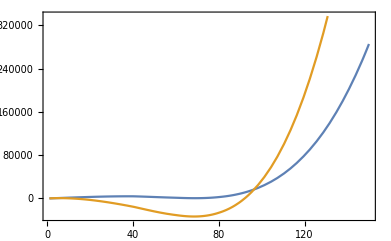

```mathematica
Ttest=66.9;
Plot[{Vpath‵ALP‵form[h,Ttest],Vpath‵Sim‵form[h,Ttest]},{h,1,150}]
```

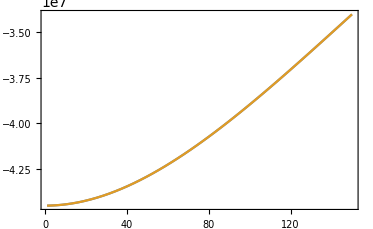

```mathematica
Plot[{VFT[h,Spath‵ALP[h,Ttest],Ttest],VFT[h,Spath‵Sim[h,Ttest],Ttest]},{h,1,150}]
```

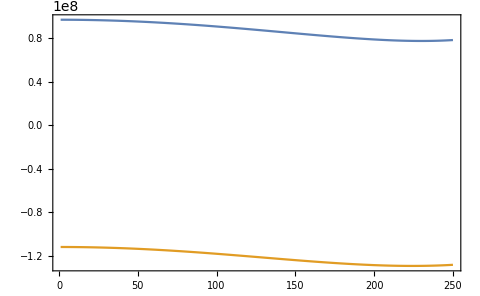

```mathematica
Plot[{V‵ALP‵0/.{v->v/(√2)}/.{v->vnum}/.benchmark/.sol‵ALP/.{S->Spath‵ALP[h,Ttest]},V‵Sim‵0/.{v->v/(√2)}/.{v->vnum}/.benchmark/.sol‵ALP/.{S->Spath‵ALP[h,Ttest]}},{h,1,250}]
```

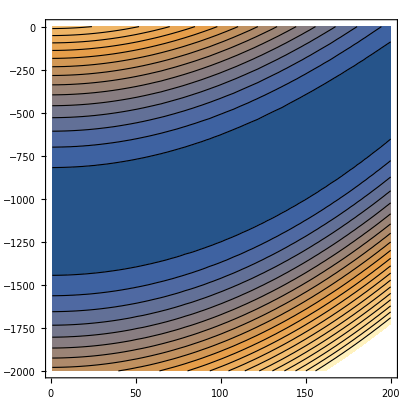

```mathematica
ContourPlot[Vtot‵ALP[h,S,Ttest],{h,1,200},{S,-2000,0},Contours->20]
```

```mathematica
Series[Cos[ϕ+δ],{ϕ,0,2}]
```

cos(δ)-ϕ sin(δ)-1/2 ϕ^2 cos(δ)+O(ϕ^3)